https://mathematica.stackexchange.com/questions/137892/reduce-a-set-expression-in-mahematica/137917#137917
https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
https://reference.wolfram.com/language/guide/LogicAndBooleanAlgebra.html
https://mathematica.stackexchange.com/questions/101819/how-can-i-define-operators-that-implement-the-algebra-of-sets
https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
https://mathematica.stackexchange.com/questions/88629/simplify-set-theoretic-expressions/88647
https://mathematica.stackexchange.com/questions/5325/define-a-mathematical-set
https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616

```mathematica
BoolTable[f_Function]:=(
Clear[x,y];
Column[{TableForm[BooleanTable[{x,y,f[x,y]},{x,y}],TableHeadings->{None,{x,y,f[x,y]}}],BooleanConvert[f[x,y],NOR],BooleanMinimize[f[x,y]]}])
BoolTable[f_]:= BoolTable[Function[f]]

BoolTable[f_Function,v_]:=(
Clear[p,q,r];
Column[{TableForm[BooleanTable[Flatten[{v,f[v]}],v],TableHeadings->{None,Flatten[{v,f[v]}]}],BooleanConvert[f[v],NOR],BooleanMinimize[f[v]]}])
BoolTable[f_,v_]:=BoolTable[Function[f],v]
```

```mathematica
Approximate2[r_,nConvergents_:8,precision_:10]:=With[{c=Convergents[ContinuedFraction[r,nConvergents]]},TableForm[Transpose[{c,N[r-c,precision]}],TableHeadings->{None,{Row[{"approximation of ",r}],"error"}}]]
```

```mathematica
ListVariables:=Names["Global`*"]
```

```mathematica
Clear[BigO]
BigO[expr_List,var_Symbol,func_]:=O[var]^func[Exponent[#-Coefficient[#,var,0],var,func]&/@expr]

Clear[MinBigO]
MinBigO[expr_List,var_Symbol]:=Plus@@Thread[O[var]^Exponent[#-Coefficient[#,var,0],var,Min]&/@expr]

(*MinBigO2[var_,expr1_,expr2_]:=If[Limit[expr1/expr2,var->Infinity]==0,expr1,expr2]*)
```

```mathematica
RationalQ[x_]:=(Head[x]===Rational||IntegerQ[x]);
```

```mathematica
(*https://mathematica.stackexchange.com/questions/32876/how-to-show-factorial-in-expanded-form-with-variables*)
FactorialExpand[expr_]:=expr/. Binomial[n_,k_]:>n!/k!/(n-k)!/. Factorial[x_]:>ProductSequence[1,x];

ProductSequence/:ProductSequence[a_,b1_]/ProductSequence[a_,b2_]:=ProductSequence[b2+1,b1];

MakeBoxes[ProductSequence[a_,b_],StandardForm]^:=RowBox[{MakeBoxes[#1 #2],"...",MakeBoxes[#3 #4]}]&[a,a+1,b-1,b];
```

```mathematica
ShowSteps[exp_]:=WolframAlpha[ToString@HoldForm@InputForm@exp,PodStates->{"Input__Step-by-step solution","Input__Show all steps"}]
SetAttributes[ShowSteps,HoldAll]
```

```mathematica
VennDiagram[x_] :=WolframAlpha[CleanStr[x],{{"VennDiagram",1},"Content"}]
SetAttributes[VennDiagram,HoldAll]
```

```mathematica
CleanStr[x_]:=ToString[ToString[HoldForm[x], StandardForm], CharacterEncoding->"ASCII"]
SetAttributes[CleanStr,HoldAll]
```

```mathematica
MakeBoxes[EmptySet,form_]^=TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)];
MakeBoxes[UniversalSet,form_]^=TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)];

CurrentValue[EvaluationNotebook[],InputAliases]={
"su"->"⊔",
"si"->"⊓",
"sb"->"⊏",
"bs"->"∖",
"es"->TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)],"us"->TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)]

};

ToBoolean[expr_]:=ReplaceAll[expr,{

SquareUnion->Or,
SquareIntersection->And,
SquareSubset->Implies,
OverBar->Not,
Backslash->(And[#1,!#2]&),
Equal->Equivalent,
EmptySet->False,
UniversalSet->True, 
CirclePlus->Xor
}]

SetQ[EmptySet]=True;
SetQ[UniversalSet]=True;
SetQ[_Symbol]=True;
SetQ[(Backslash|SquareUnion|SquareIntersection|OverBar)[a__]]:=AllTrue[{a},SetQ]
SetQ[_]=False;

FromBoolean[expr_]:=ReplaceAll[expr,{
Or->SquareUnion,
And->SquareIntersection,
Not->OverBar,
Equivalent->Equal, 
Xor->CirclePlus, 
Implies->SquareSubset
}]

FromBoolean[a_&&!b_Symbol]:=Backslash[a,b]
FromBoolean[!a_Symbol&&b_]:=Backslash[b,a]
FromBoolean[a_||!b_Symbol]:=SquareSubset[b,a]
FromBoolean[!a_Symbol||b_]:=SquareSubset[a,b]
FromBoolean[(b_&&!a_)||(a_&&!b_)]:=CirclePlus[a,b]
FromBoolean[(a_||b_)&&!(b_&&a_)]:=CirclePlus[a,b]
FromBoolean[a_⊻b_]:=CirclePlus[a,b]

(*(A∖B)⊔(B∖A)*)
Options[SetSimplify]={Method->Automatic};

(* Minimize *)
SetSimplify[set_,cond_:True,OptionsPattern[]]:=Module[{res},res=FromBoolean@BooleanMinimize[ToBoolean[set],ToBoolean[cond],Method->OptionValue[Method]];
If[SetQ[set],res/. {False->EmptySet,True->UniversalSet},res]
]

(* Simplify *)
FullSetSimplify[set_]:= FromBoolean[Simplify[ToBoolean[set]]]
```

```mathematica
(* Adapted from https://mathematica.stackexchange.com/questions/101819/how-can-i-define-operators-that-implement-the-algebra-of-sets *)
(*https://mathematica.stackexchange.com/questions/5325/define-a-mathematical-set*)
SetAttributes[set,{Flat,Orderless}]

(**)
set[args___]:=Block[{union},union=Union[{args}];
(set@@union)/;Length[union]!=Length[{args}]]

set/:Union[s___set]:=set[s]
set/:Element[e_,s_set]:=MemberQ[s,e]
set/:Subset[s___set]:=VectorQ[Partition[Reverse[{s}],2,1],SubsetQ@@#&]
set /: NotSubset[s___set]:=!TrueQ[Subset[s,#&]]
set /:Backslash[a___set,b___set]:=Complement[a,b]

(*set /: OverBar[s___set]:=Complement[s]*)
(*set /:Power[s___set,_Symbol]:=Complement[s]*)

(*https://mathematica.stackexchange.com/questions/4466/symmetric-difference-of-a-sample-of-lists*)
set /: CirclePlus[a___set,b___set]:=Complement[Union[a,b],Intersection[a,b]]

(*Needs["Combinatorica`"]*)

(* Adapted from Combinatorica CartesianProduct function implementation *)
CartesianProduct[a_,b_]:=Sort[Flatten[Outer[List,a,b,1,1],1]]

set /: Cross[a___set,b___set]:=CartesianProduct[a,b]

SetCardinality[s_set]:=Length[s]
SetCardinality[_]=0;

SetPartitions[x_]:=ResourceFunction["SetPartitions"][x]
PowerSet[x_]:=Subsets[x]

(*⟨args⟩*)
set/:MakeBoxes[s:set[args__],fmt_]:=MakeBoxes[Interpretation[{args},s],fmt]
set/:MakeBoxes[set[],fmt_]:=MakeBoxes[Interpretation["∅",set[]],fmt]
```

```mathematica
GetBinaryDataTypes[x_]:=WolframAlpha[StringJoin[ToString[x]," binary"], {{"HardwareDataTypes",1},"Content"}]
```

```mathematica
nPr[n_,r_]:=n!/(n-r)!;
(*nPr[n_,r_]:=r!nCr[n,r]*)
nCr[n_,r_]:=(n!)/(r!(n-r)!)
```

```mathematica
$UserBaseDirectory
```

```mathematica
SystemOpen["C:\\Users\\Deci\\AppData\\Roaming\\Mathematica"]
```

```mathematica
ResourceFunction["DraculaTheme"]["Install"]
```

✓ Stylesheet installed. Please restart your application.

```mathematica
(*SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Dracula.nb"]],Cell[StyleData["Input"],AutoStyleOptions->{"CommentStyle"->{FontFamily->"Consolas",FontSize->12,FontWeight->Normal}}]},Visible->False,StyleDefinitions->"PrivateStylesheetFormatting.nb"]];*)
```

```mathematica
<<Combinatorica`
```

```mathematica
Plot[x^ⅇ]
```

```mathematica
Plot[x^ⅇ,x]
```

Plot::pllim: Range specification x is not of the form {x, xmin, xmax}.

Plot[x^ⅇ,x]

```mathematica
x^ⅇ
```

x^ⅇ

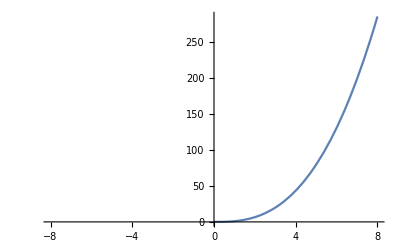

```mathematica
Plot[x^ⅇ,{x,-8,8}]
```